```mathematica
ClearAll["Global`*"]
```

3-D P-C-R system
Where we examine scale and elasticities for the dimensionless version of the system (Rstar, Cstar, Pstar are dimensionless)

Scale parameters

```mathematica
scale$αr = FullSimplify[(aR*Rstar*(1-Rstar/kR))/Rstar]
scale$αc = FullSimplify[ (λC*(Rstar/((kR/2)+Rstar))*Cstar)/Cstar]
```

aR-(aR Rstar)/kR

(2 Rstar λC)/(kR+2 Rstar)

Branching Parameters

```mathematica
branching$δ = FullSimplify[(1 - 1/scale$αc*(w*λP*Pstar*Cstar)/(Cstar*YieldP*YieldC*kR))]
branching$β = FullSimplify[(1/scale$αc*1/branching$δ*((μC*Cstar)/Cstar))]
```

1-(Pstar (kR+2 Rstar) w λP)/(2 kR Rstar YieldC YieldP λC)

(kR (kR+2 Rstar) YieldC YieldP μC)/(2 kR Rstar YieldC YieldP λC-Pstar (kR+2 Rstar) w λP)

Elasticities

```mathematica
elasticity$fr=FullSimplify[(Rstar/(aR*Rstar*(1-Rstar/kR)))*((D[aR*R*(1-R/kR),R])/.R->Rstar)]
```

2+kR/(-kR+Rstar)

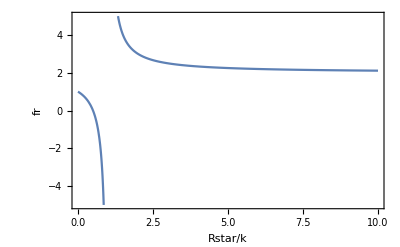

```mathematica
Plot[2+1/(-1+x),{x,0,10},PlotRange->{-5,5},Frame->True,FrameLabel->{"Rstar/k","fr"}]
```

```mathematica
elasticity$gr=FullSimplify[(Rstar/(λC*(Rstar/((kR/2)+Rstar))*Cstar))*((D[λC*(R/((kR/2)+R))*C,R])/.{R->Rstar,C->Cstar})]
```

kR/(kR+2 Rstar)

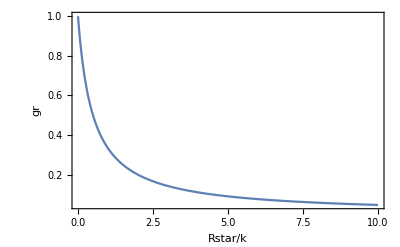

```mathematica
Plot[1/(1+2*x),{x,0,10},PlotRange->All,Frame->True,FrameLabel->{"Rstar/k","gr"}]
```

```mathematica
elasticity$gc=FullSimplify[(Cstar/(λC*(Rstar/((kR/2)+Rstar))*Cstar))*((D[λC*(R/((kR/2)+R))*C,C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
(*elasticity$sr=FullSimplify[(R/(σC*C)/.{R->Rstar,C->Cstar})*((D[σC*C,R])/.{R->Rstar,C->Cstar})]*)
```

```mathematica
elasticity$sc=FullSimplify[(Cstar/(σC*Cstar(1-Rstar/kR)))*((D[σC*C*(1-R/kR),C])/.{R->Rstar,C->Cstar})]
```

1

```mathematica
elasticity$sr=FullSimplify[(Rstar/(σC*Cstar(1-Rstar/kR)))*((D[σC*C*(1-R/kR),R])/.{R->Rstar,C->Cstar})]
```

-Rstar/(kR-Rstar)

```mathematica
elasticity$bc = FullSimplify[(Cstar/(w*λP/(YieldC*YieldP*kR)*Pstar*Cstar))*((D[w*λP/(YieldC*YieldP*kR)*P*C,C])/.{P->Pstar,C->Cstar})]
```

1

```mathematica
elasticity$mc = FullSimplify[(Cstar/(μC*Cstar))*((D[μC*C,C])/.{C->Cstar})]
```

1

```mathematica
J11 = FullSimplify[scale$αc*(elasticity$gc-(branching$δ*(branching$β*elasticity$mc+(1-branching$β)*elasticity$sc)*(1-branching$δ)*elasticity$bc))]
J12 = FullSimplify[scale$αc*(elasticity$gr-branching$δ*(1-branching$β)*elasticity$sr)]
J21 = FullSimplify[-scale$αc*elasticity$gc]
J22 = FullSimplify[scale$αr *(elasticity$fr-elasticity$gr)]
```

(2 Rstar λC)/(kR+2 Rstar)+(Pstar w λP (-2 kR Rstar YieldC YieldP λC+Pstar (kR+2 Rstar) w λP))/(2 kR^2 Rstar YieldC^2 YieldP^2 λC)

(Rstar (2 kR^3 YieldC YieldP λC+4 kR Rstar^2 YieldC YieldP λC-kR^2 Pstar w λP-4 kR Pstar Rstar w λP-4 Pstar Rstar^2 w λP-kR (kR+2 Rstar)^2 YieldC YieldP μC))/(kR (kR-Rstar) (kR+2 Rstar)^2 YieldC YieldP)

-(2 Rstar λC)/(kR+2 Rstar)

(aR (kR-4 Rstar) Rstar)/(kR (kR+2 Rstar))

```mathematica
JOnDiagonal = FullSimplify[J11*J22]
JOffDiagonal = FullSimplify[J12*J21]
```

(aR (kR-4 Rstar) Rstar ((2 Rstar λC)/(kR+2 Rstar)+(Pstar w λP (-2 kR Rstar YieldC YieldP λC+Pstar (kR+2 Rstar) w λP))/(2 kR^2 Rstar YieldC^2 YieldP^2 λC)))/(kR (kR+2 Rstar))

(2 Rstar^2 λC (-2 kR^3 YieldC YieldP λC-4 kR Rstar^2 YieldC YieldP λC+kR^2 Pstar w λP+4 kR Pstar Rstar w λP+4 Pstar Rstar^2 w λP+kR (kR+2 Rstar)^2 YieldC YieldP μC))/(kR (kR-Rstar) (kR+2 Rstar)^3 YieldC YieldP)

```mathematica
JacobianGeneral2D={
{ αc*(gc-(δ*(β*mc+(1-β)*sc)+(1-δ)*bc)),αc*(gr-δ*(1-β)*sr)},
{-αr*gc,αr*(fr-gr)}};
JacobianGeneral2D//MatrixForm
```

(αc (gc-bc (1-δ)-(sc (1-β)+mc β) δ) | αc (gr-sr (1-β) δ)
-gc αr | (fr-gr) αr)

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->w*bP[M]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],σ->σ[M],bP->w*bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[4]]
Rsol = R/.LVSS[[4]]
```

-1/(4 λ[M] σ[M]^2)α Y[M] (2 kRes (w bP[M]-λ[M]+μ[M])^2+kRes (3 w bP[M]-λ[M]+3 μ[M]) σ[M]+w bP[M] √(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2))-λ[M] √(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2))+μ[M] √(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2)))

(kRes (2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])+√(kRes^2 (8 σ[M] (w bP[M]+μ[M]+σ[M])+(2 w bP[M]-2 λ[M]+2 μ[M]+σ[M])^2)))/(4 σ[M])

```mathematica
JacobianFullModel=({
{D[eqnC,C],D[eqnC,R]},
{D[eqnR,C],D[eqnR,R]}})/.{C->Csol,R->Rsol};
```

```mathematica
data =  Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPred_fit_table_revreps.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*USING BENGUELA RELATIONSHIP - SHOULD REMEMBER THAT IT IS A VERY ROUGH ESTIMATE!*)
(*ppmrslope =0.074;
ppmrint = Exp[(184.162)]*((1/1000)^ppmrslope)*1000;*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^γ1;
massMusclegrams[M_]:=0.38*M^ζ;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

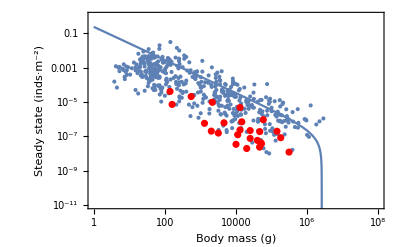

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.w->1,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

```mathematica
JacobianSpecific2D =FullSimplify[JacobianGeneral2D/.{
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
mc->elasticity$mc
}];
JacobianSpecific2D//MatrixForm
```

(0 | (Rstar (2 kR^3 YieldC YieldP λC+4 kR Rstar^2 YieldC YieldP λC-kR^2 Pstar w λP-4 kR Pstar Rstar w λP-4 Pstar Rstar^2 w λP-kR (kR+2 Rstar)^2 YieldC YieldP μC))/(kR (kR-Rstar) (kR+2 Rstar)^2 YieldC YieldP)
aR (-1+Rstar/kR) | (aR (kR-4 Rstar) Rstar)/(kR (kR+2 Rstar)))

```mathematica
JacobianAllometric2D =(JacobianSpecific2D/.{
Rstar -> Rsol,
Cstar->Csol,
Pstar->PredDensity[OptPredMass[M]]})/.{
w->1,
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α,
kR->kRes,
YieldC->Y[M],
YieldP->Ypred[OptPredMass[M],M]
};
```

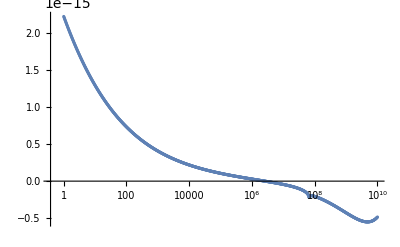

```mathematica
ListLogLinearPlot[
EigTable=Table[
{10^i,Det[(JacobianAllometric2D/.{M->(10^i)(*,bc->1*)})]},
{i,0,10,0.01}]
]
```

```mathematica
ListLogLinearPlot[
EigTableFull=ParallelTable[
{10^i, Det[(JacobianFullModel/.{M->(10^i),w->1})]},
{i,0,10,0.01}],PlotRange->All
]
```

-Graphics-

```mathematica
TCbcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,bc]]
```

{{bc→(-fr gc+(fr sc-gr sc+gc sr+(fr-gr) (mc-sc) β-gc sr β) δ)/((fr-gr) (-1+δ))}}

```mathematica
TCbcSpec = FullSimplify[TCbcGen/.{
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
(*bc->elasticity$bc,*)
mc->elasticity$mc
}];
```

```mathematica
TCbcAllo=(TCbcSpec/.{
Rstar -> Rsol,
Cstar->Csol,
Pstar->PredDensity[OptPredMass[M]]})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α,
kR->kRes,
YieldC->Y[M],
YieldP->Ypred[OptPredMass[M],M]
};
```

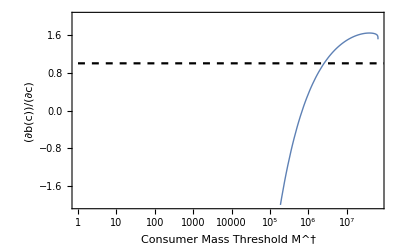

```mathematica
bcElasticityPlot=Show[{
LogLinearPlot[(bc/.TCbcAllo)/.{w->1},{M,10^0,10^8},Frame->True,FrameLabel->{"Consumer Mass Threshold M^†","(∂b(c))/(∂c)"},PlotRange->{-2,2},LabelStyle->Directive[FontSize->16],RotateLabel->False,PlotStyle->Directive[{Thick,ColorData[97,1]}]],
LogLinearPlot[1,{M,10^0,10^8},PlotStyle->Directive[{Black,Dashed}]]
}]
```

```mathematica
TCdeltaGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,δ]]
```

{{δ→(-fr gc+bc (fr-gr))/((fr-gr) (bc-sc)-gc sr-(fr-gr) (mc-sc) β+gc sr β)}}

```mathematica
TCdeltaSpec = FullSimplify[TCdeltaGen/.{
αc->scale$αc,
αr->scale$αr,
(*δ->branching$δ,*)
β->branching$β,
fr->elasticity$fr,
gr->elasticity$gr,
gc->elasticity$gc,
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
mc->elasticity$mc
}];
TCdeltaAllo=(TCdeltaSpec/.{
Rstar -> Rsol,
Cstar->Csol,
Pstar->PredDensity[OptPredMass[M]]})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α,
kR->kRes,
YieldC->Y[M],
YieldP->Ypred[OptPredMass[M],M]
};
```

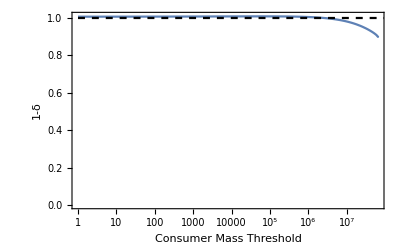

```mathematica
Show[{
LogLinearPlot[((1-δ)/.TCdeltaAllo)/.{w->1},{M,10^0,10^8},Frame->True,FrameLabel->{"Consumer Mass Threshold","1-δ"},PlotRange->{0,1.01}],
LogLinearPlot[1,{M,10^0,10^8},PlotStyle->Directive[{Black,Dashed}]]
}]
```

```mathematica
TCbcgcSpec = FullSimplify[TCbcGen/.{
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
fr->elasticity$fr,
gr->elasticity$gr,
(*gc->elasticity$gc,*)
sr->elasticity$sr,
sc->elasticity$sc,
(*bc->elasticity$bc,*)
mc->elasticity$mc
}];
TCbcgcAllo=(TCbcgcSpec/.{
Rstar -> Rsol,
Cstar->Csol,
Pstar->PredDensity[OptPredMass[M]]})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α,
kR->kRes,
YieldC->Y[M],
YieldP->Ypred[OptPredMass[M],M]
};
```

```mathematica
Plot3D[(bc/.TCbcgcAllo)/.{w->1,M->10^i},{i,0,8},{gc,-2,2},AxesLabel->{"Consumer Mass Threshold","gc","bc"},PlotRange->{-2,2}]
```

-Graphics3D-

```mathematica
TCgcGen=FullSimplify[Solve[Det[JacobianGeneral2D]==0,gc]]
```

{{gc→-((fr-gr) (bc (-1+δ)+sc (-1+β) δ-mc β δ))/(fr+sr (-1+β) δ)}}

```mathematica
TCgcSpec = FullSimplify[TCgcGen/.{
αc->scale$αc,
αr->scale$αr,
δ->branching$δ,
β->branching$β,
fr->elasticity$fr,
gr->elasticity$gr,
(*gc->elasticity$gc,*)
sr->elasticity$sr,
sc->elasticity$sc,
bc->elasticity$bc,
mc->elasticity$mc
}];
TCgcAllo=(TCgcSpec/.{
Rstar -> Rsol,
Cstar->Csol,
Pstar->PredDensity[OptPredMass[M]]})/.{
(*w->1,*)
λC->λ[M],
λP->λPred[OptPredMass[M]],
σC->σ[M],
μC->μ[M],
aR->α,
kR->kRes,
YieldC->Y[M],
YieldP->Ypred[OptPredMass[M],M]
};
```

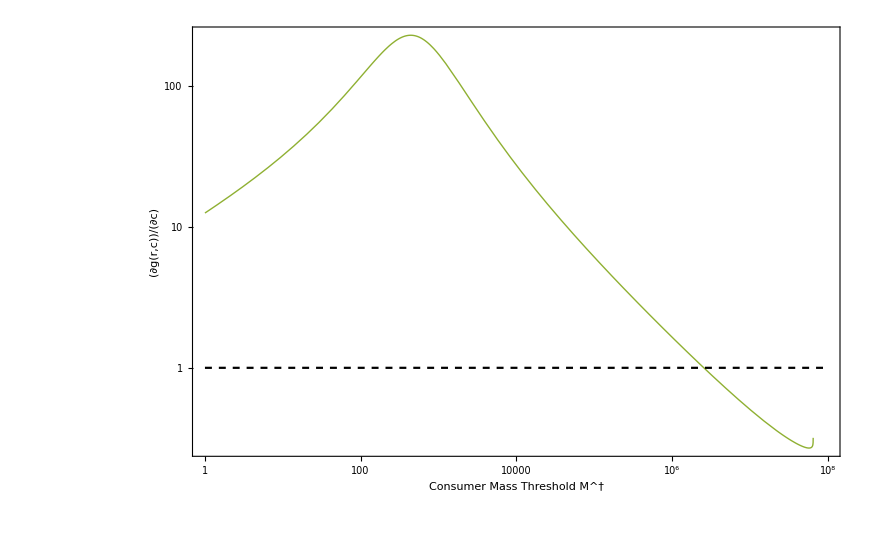

```mathematica
gcElasticityPlot=Show[{
LogLogPlot[(gc/.TCgcAllo)/.{w->1},{M,10^0,10^8},Frame->True,FrameLabel->{"Consumer Mass Threshold M^†","(∂g(r,c))/(∂c)"},PlotRange->All,LabelStyle->Directive[FontSize->16],PlotStyle->Directive[{Thick,ColorData[97,3]}],RotateLabel->False],
LogLogPlot[1,{M,10^0,10^8},PlotStyle->Directive[{Black,Dashed}]]
}]
```

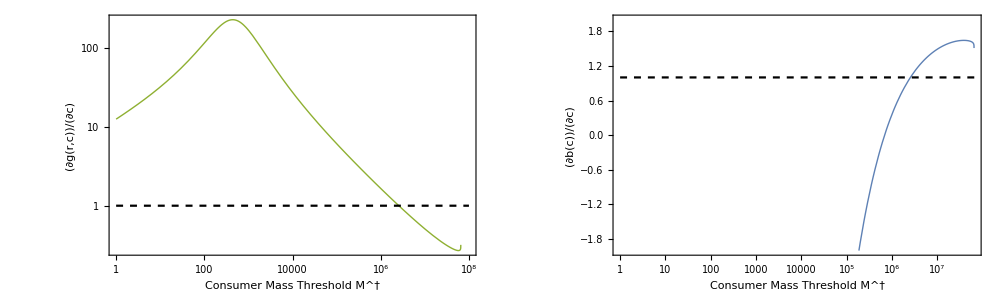

```mathematica
ElasticityPlot=GraphicsRow[{gcElasticityPlot,bcElasticityPlot},ImageSize->1000]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_elasticities_gc_bc.pdf"}],ElasticityPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_elasticities_gc_bc.pdf

```mathematica
Solve[D[(gc/.TCgcAllo)/.{w->1},M]==0,M]
```

$Aborted